Ryan Hill (rjh324@cornell.edu)
E. Fadaly, A. Dijkstra, J. Suckert, et al., Direct-bandgap emission 
from hexagonal Ge and SiGe alloys, Nature 580, 205 (2020).

### Tight Binding Model

```mathematica
(*Material properties*)
SiVals = {Esa->-4.2, Epa->1.715,Esc->-4.2, Epc->1.715,Essa->6.685, Essc->6.685, Vss->-8.3, Vxx->1.715, Vxy->4.575, Vsapc->5.7292, Vpasc->5.7292, Vssapc->5.3749, Vpassc->5.3749, Vssss->0,aL->5.431*10^-10};
GeVals = {Esa->-5.88, Epa->1.61,Esc->-5.88, Epc->1.61,Essa->6.39, Essc->6.39, Vss->-6.78, Vxx->1.61, Vxy->4.9, Vsapc->5.4649, Vpasc->5.4649, Vssapc->5.2191, Vpassc->5.2191, Vssss->0,aL->5.658*10^-10};
```

```mathematica
(*Matrix Elements*)
g0[k_]:=Cos[k[[1]]*aL/4]*Cos[k[[2]]*aL/4]*Cos[k[[3]]*aL/4]-ⅈ*Sin[k[[1]]*aL/4]*Sin[k[[2]]*aL/4]*Sin[k[[3]]*aL/4];
g1[k_]:=-Cos[k[[1]]*aL/4]*Sin[k[[2]]*aL/4]*Sin[k[[3]]*aL/4]+ⅈ*Sin[k[[1]]*aL/4]*Cos[k[[2]]*aL/4]*Cos[k[[3]]*aL/4];
g2[k_]:=-Sin[k[[1]]*aL/4]*Cos[k[[2]]*aL/4]*Sin[k[[3]]*aL/4]+ⅈ*Cos[k[[1]]*aL/4]*Sin[k[[2]]*aL/4]*Cos[k[[3]]*aL/4];
g3[k_]:=-Sin[k[[1]]*aL/4]*Sin[k[[2]]*aL/4]*Cos[k[[3]]*aL/4]+ⅈ*Cos[k[[1]]*aL/4]*Cos[k[[2]]*aL/4]*Sin[k[[3]]*aL/4];
g0s[k_]:=Conjugate[g0[k]];
g1s[k_]:=Conjugate[g1[k]];
g2s[k_]:=Conjugate[g2[k]];
g3s[k_]:=Conjugate[g3[k]];
```

```mathematica
(*Hamiltonian*)
H[k_]:={{Esa,Vss*g0[k],0,0,0,Vsapc*g1[k],Vsapc*g2[k],Vsapc*g3[k],0,0},{Vss*g0s[k],Esc,-Vpasc*g1s[k],-Vpasc*g2s[k],-Vpasc*g3s[k],0,0,0,0,0},{0,-Vpasc*g1[k],Epa,0,0,Vxx*g0[k],Vxy*g3[k],Vxy*g2[k],0,-Vpassc*g1[k]},
{0,-Vpasc*g2[k],0,Epa,0,Vxy*g3[k],Vxx*g0[k],Vxy*g1[k],0,-Vpassc*g2[k]},{0,-Vpasc*g3[k],0,0,Epa,Vxy*g2[k],Vxy*g1[k],Vxx*g0[k],0,-Vpassc*g3[k]},{Vsapc*g1s[k],0,Vxx*g0s[k],Vxy*g3s[k],Vxy*g2s[k],Epc,0,0,Vssapc*g1[k],0},{Vsapc*g2s[k],0,Vxy*g3s[k],Vxx*g0s[k],Vxy*g1s[k],0,Epc,0,Vssapc*g2[k],0},{Vsapc*g3s[k],0,Vxy*g2s[k],Vxy*g1s[k],Vxx*g0s[k],0,0,Epc,Vssapc*g3[k],0},{0,0,0,0,0,Vssapc*g1s[k],Vssapc*g2s[k],Vssapc*g3s[k],Essa,Vssss*g0[k]},{0,0,-Vpassc*g1s[k],-Vpassc*g2s[k],-Vpassc*g3s[k],0,0,0,Vssss*g0s[k],Essc}};
```

```mathematica
(*Lattice and reciprocal lattice vectors*)
a1=aL*{1/2,1/2,0};
a2=aL*{1/2,0,1/2};
a3=aL*{0,1/2,1/2};

b1=2*π*((a2×a3)/(a1.(a2×a3)));
b2=2*π*((a3×a1)/(a2.(a3×a1)));
b3=2*π*((a1×a2)/(a3.(a1×a2)));
```

```mathematica
(*k-space path: X-> Γ -> L*)
Γ={0,0,0};
X=b2/2+b3/2;
L=b1/2+b2/2+b3/2;

XΓ=1000;
ΓL=1000*Norm[L-Γ]/Norm[Γ-X];

XtoΓ=Table[X+t/XΓ*(Γ-X),{t,0,1000,1}];
ΓtoL=Table[Γ+t/ΓL*(L-Γ),{t,0,ΓL,1}];

k=Join[XtoΓ,ΓtoL];
```

```mathematica
(*Eigenvalues*)
SiEnergies=Table[Eigenvalues[H[k[[t]]]/.SiVals],{t,1,Length[k]-1}];
GeEnergies=Table[Eigenvalues[H[k[[t]]]/.GeVals],{t,1,Length[k]-1}];
```

```mathematica
(*Plot*)
Sikmin=-Norm[Γ-X]/.SiVals;
Sikmax=Norm[L-Γ]/.SiVals;
Gekmin = -Norm[Γ-X]/.GeVals;
Gekmax = Norm[L-Γ]/.GeVals;

Xpoint=0;
Γpoint=1000;
Lpoint=1866.025;
```

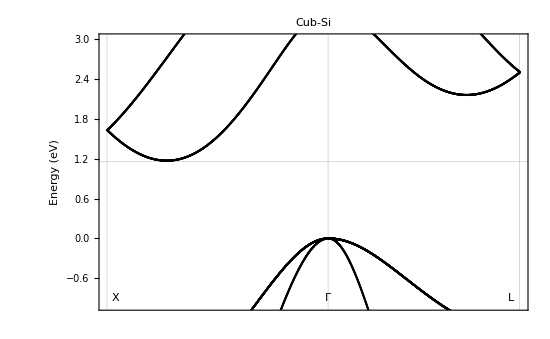

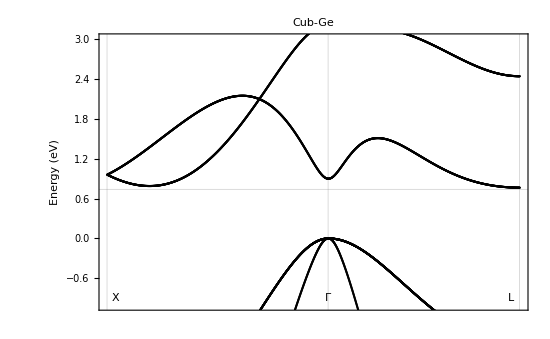

```mathematica
Show[ListPlot[Transpose[SiEnergies],PlotStyle->Black,GridLines->{{Xpoint,Γpoint,Lpoint},{1.16}},Frame->{{True,True},{True,True}},FrameTicks->{None,Automatic},Axes->{True,False},TicksStyle->Opacity[0],PlotLabel->"Cub-Si",FrameLabel->{None,"Energy (eV)"},LabelStyle->Directive[Black,16]],Epilog->{Text["Γ",{Γpoint,-0.9}],Text["L",{Lpoint-40,-0.9}],Text["X",{Xpoint+40,-0.9}]},PlotRange->{-1,3},PlotRangePadding->0,ImageSize->550]

Show[ListPlot[Transpose[GeEnergies],PlotStyle->Black,GridLines->{{Xpoint,Γpoint,Lpoint},{0.74}},Frame->{{True,True},{True,True}},FrameTicks->{None,Automatic},Axes->{True,False},TicksStyle->Opacity[0],PlotLabel->"Cub-Ge",FrameLabel->{None,"Energy (eV)"},LabelStyle->Directive[Black,16]],Epilog->{Text["Γ",{Γpoint,-0.9}],Text["L",{Lpoint-40,-0.9}],Text["X",{Xpoint+40,-0.9}]},PlotRange->{-1,3},PlotRangePadding->0,ImageSize->550]
```

### Temperature dependence of the fundamental bandgap

```mathematica
Eg1[T_]:=a-b(1+2/(ⅇ^(θ/T)-1));
Eg2[T_]:=c-d(1+2/(ⅇ^(γ/T)-1));
```

```mathematica
a=0.358  (*eV*);
b=0.0072 (*eV*);
θ=67 (*Kelvin*);
c=0.378;
d=0.0063;
γ=55;
energies1=Table[{T,Eg1[T]},{T,0,300,10}];
energies2=Table[{T,Eg2[T]},{T,0,300,10}];
```

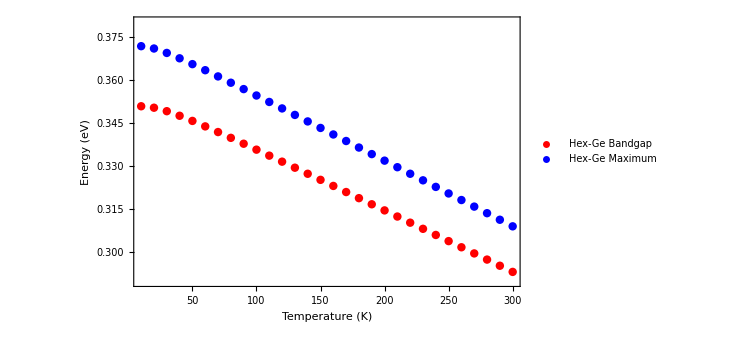

```mathematica
Show[ListPlot[{energies1,energies2},PlotStyle->{Red,Blue},PlotLegends->LineLegend[{Red,Blue},{"Hex-Ge Bandgap", "Hex-Ge Maximum"}]],Frame->{{True,True},{True,True}},FrameTicks->{Automatic,Automatic},Axes->{True,False},TicksStyle->Opacity[0],FrameLabel->{"Temperature (K)","Energy (eV)"},LabelStyle->Directive[Black,16],PlotRange->{0.29,0.38},PlotRangePadding->0,ImageSize->550]
```

### Temperature dependence of the photoluminescence spectra